3

12

9

7

8

9

10

13

10

17

35

23

{{1,2.69949},{2,2.974},{3,2.80541},{4,3.05671},{5,3.06742},{6,3.1769},{7,2.97923},{8,3.22624},{9,3.13835},{10,2.94379},{11,3.128},{12,2.95224}}

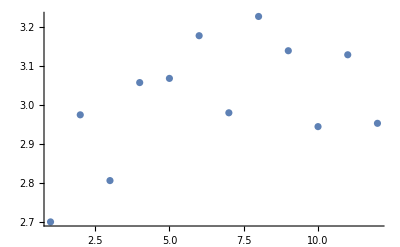

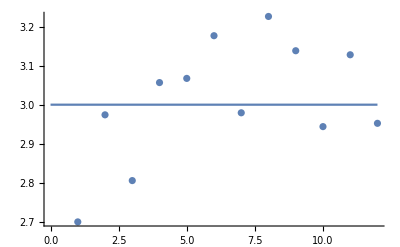

```mathematica
(*twice Number of plaquettes*)

L=40;
R0=3;
T0=1;
wilsonlink[β_]:=Module[{F1,F2,h1,h2,act1,act2,plaq,a1,a2,r,g,ftest,f,J,ϵ},(*Initial lattice config.*)

F1=Table[If[Xor[EvenQ[i],EvenQ[j]],1,0],{i,L},{j,L}];
F2=Table[If[Xor[EvenQ[i],EvenQ[j]],Exp[I*RandomReal[{-Pi,Pi}]],0],{i,L},{j,L}];
(*Wilson Loop 1x1 Action*)h1[k_,i_,j_]:=Module[{p},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
1-Re[p[1,0]**p[2,1]**p[1,2]*p[0,1]]];
(*WilsonLoopRxT*)h2[k_,i_,j_,R_,T_]:=Module[{p},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
Re[Product[p[x,0]**p[x,2T],{x,1,2R,2}]*Product[p[0,x]*(p[2R,x])*,{x,1,2T,2}]]];
plaq[k_]:=Table[h1[k,i,j],{i,1,L,2},{j,1,L,2}];
(*Average Action*)
act1[k_]:=Sum[If[OddQ[i]&&OddQ[j],h1[k,i,j],0],{i,L},{j,L}]/((L/2)^2);
act2[k_]:=Sum[If[OddQ[i]&&OddQ[j],(1/2)*(h2[k,i,j,R0,T0]+h2[k,i,j,T0,R0]),0],{i,L},{j,L}]/((L/2)^2);
(*Initializaze lattice data*)
a1=List[{act2[F1]},{act1[F1]},{F1}];
a2=List[{act2[F2]},{act1[F2]},{F2}];
(*"Monte Carlo" Rejection Sampling*)r[t_]:=Module[{o},While[True,o=RandomReal[{-Pi,Pi}];
If[RandomReal[]<Exp[β*t*(Cos[o]-1)],Break[]];];
Return[o]];
(*Generating Rule*)g[k_,i_,j_]:=Module[{p,d1,d2},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
d1:=p[0,-2]**p[1,-1]**p[-1,-1]+p[0,2]**p[1,1]*p[-1,1]*;
d2:=p[2,0]**p[1,1]*p[1,-1]*+p[-2,0]**p[-1,-1]*p[-1,1]*;
Which[
EvenQ[i]&&OddQ[j],Exp[I*r[Abs[d1]]]*(d1*/Abs[d1]),
EvenQ[j]&&OddQ[i],Exp[I*r[Abs[d2]]]*(d2*/Abs[d2]),
True,0]];


ftest[k_]:=Module[{s},s=Table[If[k[[i,j]]==0,0,Arg[k[[i,j]]]],{i,L},{j,L}]];


f[m_]:=Module[{s},
s=m;
For[i=1,i<L+1,i++,
For[j=1,j<L+1,j++,
s[[i,j]]=g[s,i,j];
];];
s
];

(*Run Simulation max J Times*)
J=50;
ϵ=0.03;
For[k=0,k<J,k++,
F1=f[F1];
a1[[1]]=Append[a1[[1]],act2[F1]];
a1[[2]]=Append[a1[[2]],act1[F1]];
a1[[3]]=Append[a1[[3]],F1];
F2=f[F2];
a2[[1]]=Append[a2[[1]],act2[F2]];
a2[[2]]=Append[a2[[2]],act1[F2]];
a2[[3]]=Append[a2[[3]],F2];
If[Abs[(a1[[2]][[-1]]-a2[[2]][[-1]])/(a1[[2]][[-1]]+a2[[2]][[-1]])]<ϵ&&Abs[(a1[[2]][[-1]]-a1[[2]][[-2]])/(a1[[2]][[-1]]+a1[[2]][[-2]])]<ϵ&&Abs[(a2[[2]][[-1]]-a2[[2]][[-2]])/(a2[[2]][[-1]]+a2[[2]][[-2]])]<ϵ,Break[]]
];
(*Print["Trivial"];*)
(*Print[Multicolumn[MatrixPlot/@ftest/@a1[[3]],4,Appearance->"Horizontal"]];*)
(*Print[Multicolumn[MatrixForm/@plaq/@a1[[3]],4,Appearance->"Horizontal"]];*)
(*Print["Random"];*)
(*Print[Multicolumn[MatrixPlot/@ftest/@a2[[3]],4,Appearance->"Horizontal"]];*)
(*Print[Multicolumn[MatrixPlot/@plaq/@a2[[3]],4,Appearance->"Horizontal"]];*)(*Print[ListPlot[{a1[[2]],a2[[2]]},Joined->True,Mesh->Full,PlotRange->All,DataRange->All,PlotLabels->{"Trivial","Random"}]];*)
Print[Length[a1[[2]]]];
Log[(a1[[1,-1]]+a2[[1,-1]])/2]/Log[1-((a1[[2,-1]]+a2[[2,-1]])/2)]
];
range=12;
data=Table[{β,wilsonlink[β]},{β,1,range,1}]
ListPlot[data,PlotRange->All]
f[b_]:=T0*R0;
Show[Plot[f[b],{b,0,range}],ListPlot[data,PlotRange->All],PlotRange->All,AxesOrigin->{0,0}]
```